# PCTS Tutorial: Geometry of Wannier States

## Goals

Basic Numerical Tools

All Graduate Students should know

Make Abstract ideas Concrete

Understand topological and geometrical ideas by looking at wave-functions

## Reference

http://muellergroup.lassp.cornell.edu/PCTS

Disclaimer: All ideas are stolen

## How do you know that you understand something?

You can use it.

You can generalize it.

You can teach it to someone else.

You can teach it to a computer.

## Finite Differences

Calculus for sampled functions:

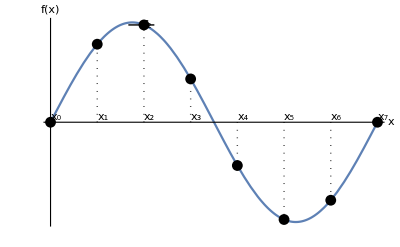

```mathematica
xdat=Table[x,{x,0,2 Pi,2 Pi/7}];
fvec=N[Sin[xdat]];
Show[Plot[Sin[x],{x,0,2 Pi}],ListPlot[Table[{x,N@Sin[x]},{x,0,2 Pi,2 Pi/7}],PlotStyle->Black],Graphics[{Table[{Text[Subscript[x, j],{2 Pi/7 j,0 Sin[2 Pi/7 j]},{-1,-1}],Black,Dotted,Line[{{2 Pi/7 j,0 Sin[2 Pi/7 j]},{2 Pi/7 j, Sin[2 Pi/7 j]}}]},{j,0,7}],
Text["f_2",{2 Pi/7 2, Sin[2 Pi/7 2]},{-3,0}],Line[{{2 Pi/7 2-0.3, Sin[2 Pi/7 2]},{2 Pi/7 2+0.2, Sin[2 Pi/7 2]}}]
}],BaseStyle->{FontSize->18},Ticks->None,AxesLabel->{"x","f(x)"}]
```

```mathematica
fvec
```

{0.,0.781831,0.974928,0.433884,-0.433884,-0.974928,-0.781831,0.}

Slopes are linear combinations of function values:

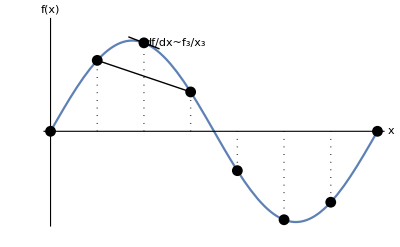

```mathematica
Show[Plot[Sin[x],{x,0,2 Pi}],ListPlot[Table[{x,Sin[x]},{x,0,2 Pi,2 Pi/7}],PlotStyle->Black],Graphics[{Table[{Black,Dotted,Line[{{2 Pi/7 j,0 Sin[2 Pi/7 j]},{2 Pi/7 j, Sin[2 Pi/7 j]}}]},{j,0,7}],
Text["df/dx~f_3/x_3",{2 Pi/7 2, Sin[2 Pi/7 2]},{-2,0}],Line[{{2 Pi/7 2-0.3, Sin[2 Pi/7 2]-0.3 Cos[2 Pi/7 2]},{2 Pi/7 2+0.3, Sin[2 Pi/7 2]+ 0.3 Cos[2 Pi/7 2]}}],
Line[{{2 Pi/7 , Sin[2 Pi/7 ]},{2 Pi/7 3, Sin[2 Pi/7 3]}}]
}],BaseStyle->{FontSize->18},Ticks->None,AxesLabel->{"x","f(x)"},PlotRange->{-1,1.2}]
```

Matrix Representation of derivative operation:

```mathematica
DerivativeMatrix[stepsize_,numsteps_Integer] := SparseArray[{Band[{2,1}]->-1/(2 stepsize),Band[{1,2}]->1/(2 stepsize)},{numsteps,numsteps}];

MatrixForm[DerivativeMatrix[(*stepsize =*)1,(*numsteps =*)10]]
```

(0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1/2 | 0 | 1/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1/2 | 0 | 1/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 1/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 1/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 1/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0)

Test it out

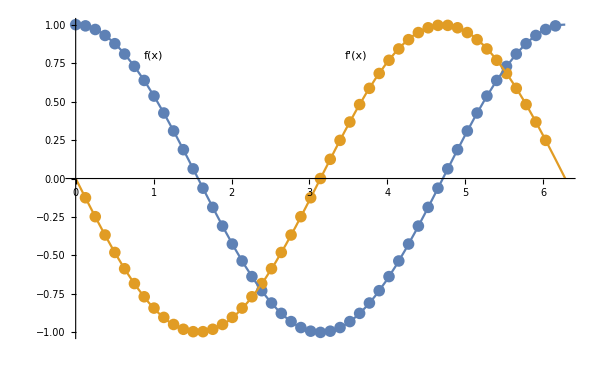

```mathematica
steps=50;  (* How Many steps *)
xgrid= Table[x,{x,0.,2 Pi-2 Pi/steps,2 Pi/steps}];  (* Make Grid *)
fdat=Cos/@xgrid;  (* Evaluate function on Grid *)
dmat=DerivativeMatrix[2. Pi/steps,steps];  (* Make matrix which takes derivative *)
derivdat=dmat.fdat;  (* Take derivative *)
Show[ListPlot[{Transpose[{xgrid,fdat}],Transpose[{xgrid,derivdat}]}],Plot[{Cos[x],-Sin[x]},{x,0,2 Pi}],
Graphics[{Text["f(x)",{1,0.8}],Text["f'(x)",{3.6,0.8}]}]
,PlotRange->{-1,1},BaseStyle->{FontSize->16}]
```

## Hamiltonian

```mathematica
hamiltonian[potential_,xmin_?NumericQ,xmax_?NumericQ,dx_?NumericQ]:=
Module[ 
(* Define Local Variables *)
{xgrid=Table[x,{x,xmin,xmax-dx,dx}],numsteps,kin,pot},
numsteps=Length[xgrid];
kin=(-0.5/dx^2)*SparseArray[{Band[{1,2}]->1,Band[{2,1}]->1,Band[{1,1}]->-2},{numsteps,numsteps}];
pot=SparseArray[Band[{1,1}]->potential/@xgrid];
kin+pot]
```

Energies of a harmonic oscillator:

```mathematica
xmin=-5;
xmax=5;
dx=0.1;
xgrid=Table[x,{x,xmin,xmax-dx,dx}];
harmonicpotential[x_]=x^2/2;
harmonicham=hamiltonian[harmonicpotential,xmin,xmax,dx];
harmspectrum=Reverse@Eigenvalues[harmonicham,5,Method->{"Arnoldi","Shift"->0}]
```

{0.499687,1.49844,2.49593,3.49217,4.48716}

Wavefunctions of a harmonic oscillator:

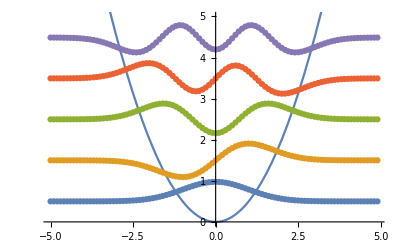

```mathematica
states=Transpose[Reverse/@Eigensystem[harmonicham,5,Method->{"Arnoldi","Shift"->0}]];
Show[Plot[x^2/2,{x,-4,4}],ListPlot[Transpose[{xgrid,#1+2 #2}]&@@@states],PlotRange->{0,5}]
```

## Double Well

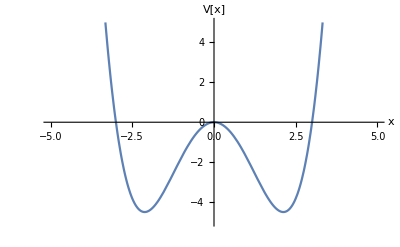

```mathematica
quadpot[x_]=2(x^4/9-x^2);
Plot[quadpot[x],{x,-5,5},PlotRange->{-5,5},AxesLabel->{"x","V[x]"},BaseStyle->{FontSize->16}]
```

States :

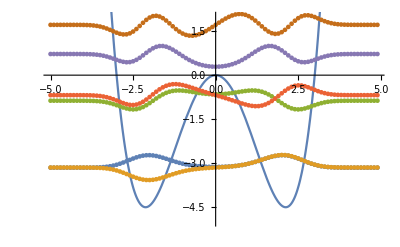

```mathematica
quadham=hamiltonian[quadpot,xmin,xmax,dx];
states=Sort@Transpose[Eigensystem[quadham,6,Method->{"Arnoldi","Shift"->-4}]];
Show[Plot[quadpot[x],{x,-4,4}],ListPlot[Transpose[{xgrid,#1+2 #2}]&@@@states],PlotRange->{-5,2}]
```

As expected, get pairs of nearly degenerate states :

```mathematica
states[[All,1]]
```

{-3.15187,-3.14775,-0.869891,-0.681844,0.720469,1.71419}

Question : How to find superposition of lowest two states which is “mostly on the right”

## Answer

Take sum/difference

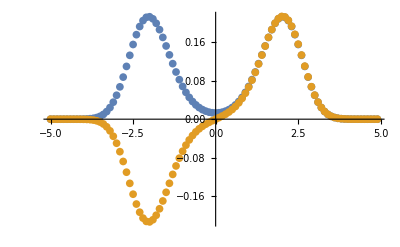

```mathematica
ListPlot[{Transpose[{xgrid,states[[1,2]]}],Transpose[{xgrid,states[[2,2]]}]}]
```

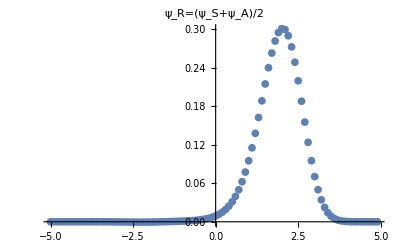

```mathematica
ListPlot[{Transpose[{xgrid,(states[[1,2]]+states[[2,2]])/Sqrt[2]}]},PlotLabel->"ψ_R=(ψ_S+ψ_A)/2"]
```

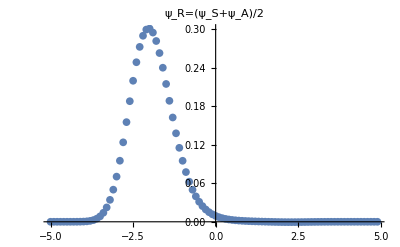

```mathematica
ListPlot[{Transpose[{xgrid,(states[[1,2]]-states[[2,2]])/Sqrt[2]}]},PlotLabel->"ψ_R=(ψ_S+ψ_A)/2"]
```

Is this unique?  How do we generalize to more sites?

## Wannier States

Wannier states = localized states which form basis for band.  Many-well analog of left and right states in double well

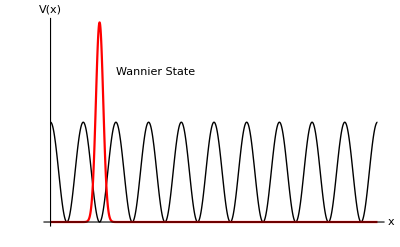

```mathematica
Plot[{Cos[x]^2,2 Exp[-4(x-3 Pi/2)^2]},{x,0,10 Pi},PlotStyle->{{Thick,Black},Red},Ticks->None,PlotRange->{0,2},AxesLabel->{"x","V(x)"},BaseStyle->{FontSize->16},Epilog->Text["Wannier State",{2 Pi, 1.5},{-1,0}]]
```

Properties:

ϕ(x-j a), j=0,1,2,... form basis for band

ϕ(x-i a) and ϕ(x-j a) are orthogonal if i≠j

These do not uniquely define ϕ -- given Bloch states ψ_k(x) can take

ϕ(x)=∑_k e^(i χ_k)ψ_k(x)

for any choice of χ_k.  Typically make ϕ as tightly peaked as possible.  [Maximally localized Wannier States.]

We will directly find ϕ without first finding Bloch states

## Double Well Problem

```mathematica
ListPlot[{Transpose[{xgrid,states[[1,2]]}],Transpose[{xgrid,states[[2,2]]}]}]
```

-Graphics-

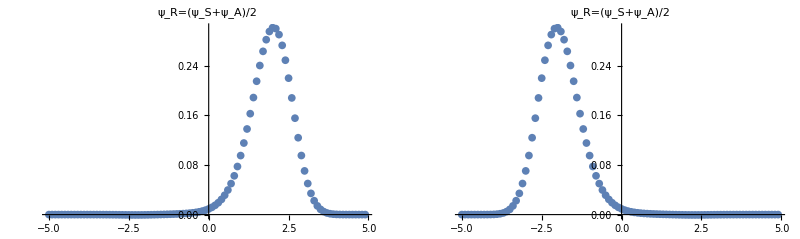

```mathematica
GraphicsGrid[{{ListPlot[{Transpose[{xgrid,(states[[1,2]]+states[[2,2]])/Sqrt[2]}]},PlotLabel->"ψ_R=(ψ_S+ψ_A)/2",BaseStyle->{FontSize->16}],ListPlot[{Transpose[{xgrid,(states[[1,2]]-states[[2,2]])/Sqrt[2]}]},PlotLabel->"ψ_R=(ψ_S+ψ_A)/2",BaseStyle->{FontSize->16}]}},ImageSize->800]
```

Less localized, but alternative “left” and “right” states (analogous to other choices of Wannier States)

ψ_L=ψ_S+e^(i χ)ψ_A

ψ_R=ψ_S-e^(i χ)ψ_A

Have correct symmetry (related by reflection), are orthogonal, but clearly not “correct” left and right states.

Rψ_S=ψ_s                       Rψ_A =-ψ_A
Rψ_L =ψ_R                      Rψ_R = ψ_L

## Projector Construction

Wannier States in 1D are eigenstates of position operator, projected into band

Numerical Creation of position operator:

```mathematica
ArrayPlot[xop=SparseArray[Band[{1,1}]->xgrid]] (* Position operator *)
```

-Graphics-

Mathematical description of position operator:

X(ψ_0
ψ_1
ψ_2
ψ_3
ψ_4)=(x_0 ψ_0
x_1 ψ_1
x_2 ψ_2
x_3 ψ_3
x_4 ψ_4)

Graphical description of position operator:

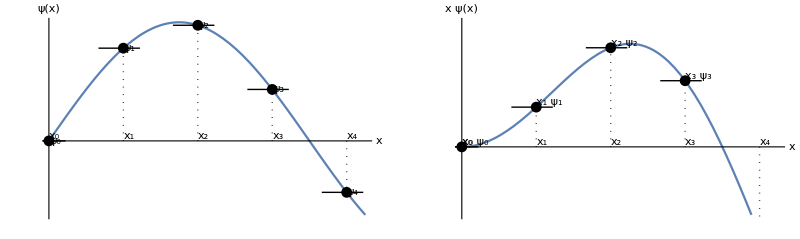

```mathematica
GraphicsGrid[{{Show[Plot[Sin[x],{x,0,8.5 Pi/7}],ListPlot[Table[{x,Sin[x]},{x,0,8.5Pi/7,2 Pi/7}],PlotStyle->Black,PlotRange->All],Graphics[{Table[{Text[Subscript[x, j],{2 Pi/7 j,0 Sin[2 Pi/7 j]},{-1,-1}],Black,Dotted,Line[{{2 Pi/7 j,0 Sin[2 Pi/7 j]},{2 Pi/7 j, Sin[2 Pi/7 j]}}]},{j,0,4}],
Table[{Text[Subscript[ψ, j],{j Pi/7 2, Sin[j Pi/7 2]},{-3,0}],Line[{{j Pi/7 2-0.3, Sin[j Pi/7 2]},{j Pi/7 2+0.2, Sin[j Pi/7 2]}}]},{j,0,4}]
}],BaseStyle->{FontSize->18},Ticks->None,AxesLabel->{"x","ψ(x)"}],
Show[Plot[x Sin[x],{x,0,8.5 Pi/7},PlotRange->{-1.2,2.2}],ListPlot[Table[{x,x Sin[x]},{x,0,8.5Pi/7,2 Pi/7}],PlotStyle->Black,PlotRange->All],Graphics[{Table[{Text[Subscript[x, j],{2 Pi/7 j,0 Sin[2 Pi/7 j]},{-1,-1}],Black,Dotted,Line[{{2 Pi/7 j,0 Sin[2 Pi/7 j]},{2 Pi/7 j,2 Pi/7 j Sin[2 Pi/7 j]}}]},{j,0,4}],
Table[{Text[Subscript[x, j] Subscript[ψ, j],{j Pi/7 2,2 Pi/7 j Sin[j Pi/7 2]},{-1,-1}],Line[{{j Pi/7 2-0.3,2 Pi/7 j Sin[j Pi/7 2]},{j Pi/7 2+0.2,2 Pi/7 j Sin[j Pi/7 2]}}]},{j,0,4}]
}],BaseStyle->{FontSize->18},Ticks->None,AxesLabel->{"x","x ψ(x)"}]}},ImageSize->800]
```

Projection operator is rectangular matrix made of states in space:

```mathematica
lowenergyspace={states[[1,2]],states[[2,2]]};
```

size of matrix:

```mathematica
Dimensions[lowenergyspace]
```

{2,100}

Meaning: 2 states in our “band”, space discretized into 100 points

Project “X” operator into this band:

```mathematica
Dimensions[projX=lowenergyspace.xop.ConjugateTranspose[lowenergyspace]]
```

{2,2}

```mathematica
MatrixForm[Chop[projX]]
```

(0 | 1.97728
1.97728 | 0)

IE. Up to terms which take you out of low energy space:
 xψ_s=1.97728 ψ_A    and     xψ_A=1.97728 ψ_S

Eigenvalues of projected X operator are the most localized states which can be made from “band.”  Eigenvectors are center-of-mas of the state.

```mathematica
esx=Eigensystem[projX]
```

{{-1.97728,1.97728},{{-0.707107,0.707107},{-0.707107,-0.707107}}}

```mathematica
XStatesInOriginalBasis=esx[[2]].lowenergyspace;
```

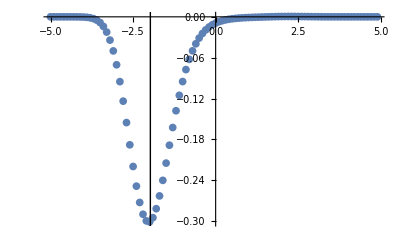

```mathematica
ListPlot[Transpose[{xgrid,XStatesInOriginalBasis[[1]]}],Epilog->Line[{{esx[[1,1]],-1},{esx[[1,1]],1}}]]
```

Effective Hamiltonian in low-energy space -- tight binding model of double-well potential

```mathematica
MatrixForm[XStatesInOriginalBasis.quadham.ConjugateTranspose[XStatesInOriginalBasis]]
```

(-3.14981 | -0.0020595
-0.0020595 | -3.14981)

## Multisite version

sevenwells[x_] = Sum[-60/Cosh[20*(x - j)], {j, -3, 3}]; 
Plot[sevenwells[x], {x, -5, 5}, AxesLabel -> {"x", "V"}, BaseStyle -> {FontSize -> 16}]

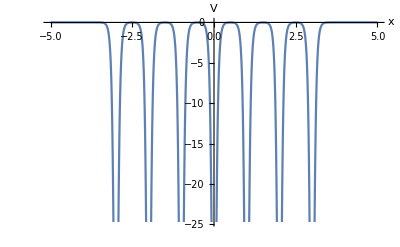

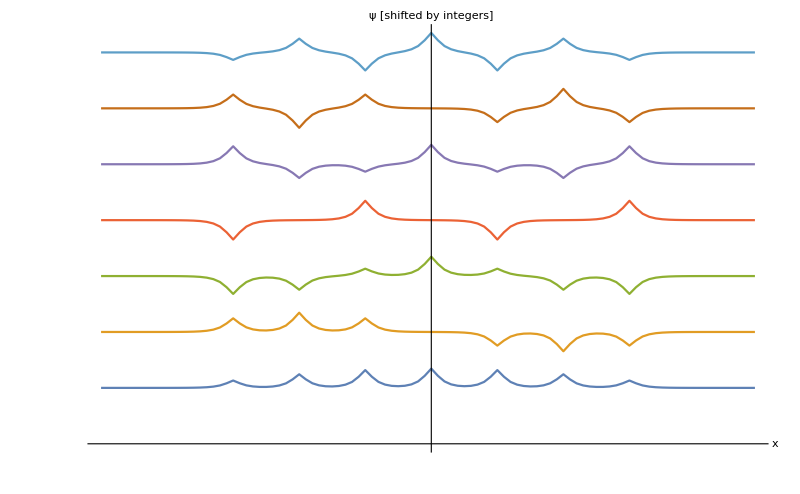

```mathematica
sevenham=hamiltonian[sevenwells,xmin,xmax,dx];
sevenstates=Sort@Transpose[Eigensystem[sevenham,7,Method->{"Arnoldi","Shift"->-50}]];
ListPlot[MapIndexed[Transpose[{xgrid,#2[[1]]+  1#1 Sign[#1[[50]]]}]&,sevenstates[[All,2]]],Joined->True, BaseStyle -> {FontSize -> 16},Ticks->None,AxesLabel->{"x","ψ [shifted by integers]"},ImageSize->800]
```

Make projector into the 7-dimensional space of low energy states:

```mathematica
Dimensions[low7=sevenstates[[All,2]]]
```

{7,100}

Project the position operator into this space

```mathematica
Dimensions[projX7=low7.xop.ConjugateTranspose[low7]]
```

{7,7}

Find eigenvalues and eigenvectors.  Eigenvectors are a local basis for the band.  Eigenvalues are the center of mass positions.

```mathematica
es7=Transpose[Sort[Transpose[Eigensystem[projX7]]]] //Chop
```

{{-3.00005,-2.,-1.,0,1.,2.,3.00005},{{-0.191281,0.353467,-0.461879,-0.5,-0.462001,0.35364,-0.191403},{-0.353539,0.500025,-0.353653,-0.000137816,0.353454,-0.499975,0.353568},{0.461959,-0.353605,-0.191288,-0.5,-0.191395,-0.353502,0.461921},{-0.500032,-3.25709×10^-10,0.500013,-4.80413×10^-10,-0.499987,-3.54754×10^-10,0.499968},{-0.461959,-0.353605,0.191288,-0.5,0.191395,-0.353502,-0.461921},{-0.353539,-0.500025,-0.353653,0.000137816,0.353454,0.499975,0.353568},{-0.191281,-0.353467,-0.461879,0.5,-0.462001,-0.35364,-0.191403}}}

```mathematica
XStatesInOriginalBasis7=es7[[2]].low7;
```

```mathematica
Dimensions[XStatesInOriginalBasis7]
```

{7,100}

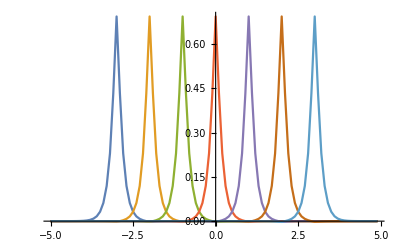

```mathematica
ListPlot[Transpose[{xgrid,# Sign[Plus@@#]}]&/@XStatesInOriginalBasis7,Joined->True,PlotRange->All]
```

Orthogonality:

```mathematica
Chop[XStatesInOriginalBasis7.ConjugateTranspose[XStatesInOriginalBasis7]]//MatrixForm
```

(1. | 0 | 0 | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0 | 0 | 0
0 | 0 | 1. | 0 | 0 | 0 | 0
0 | 0 | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 0 | 0 | 1.)

Tight binding model -- hoppings of different ranges

```mathematica
MatrixForm[Chop[XStatesInOriginalBasis7.sevenham.ConjugateTranspose[XStatesInOriginalBasis7]]]
```

(-22.4792 | -0.0722358 | -0.00058591 | -7.55762×10^-6 | 1.17277×10^-7 | -2.01164×10^-9 | 0
-0.0722358 | -22.4786 | 0.0722431 | 0.000585945 | -7.55809×10^-6 | 1.17286×10^-7 | -2.01134×10^-9
-0.00058591 | 0.0722431 | -22.4786 | 0.0722431 | -0.000585945 | 7.55809×10^-6 | -1.17277×10^-7
-7.55762×10^-6 | 0.000585945 | 0.0722431 | -22.4786 | -0.0722431 | 0.000585945 | -7.55762×10^-6
1.17277×10^-7 | -7.55809×10^-6 | -0.000585945 | -0.0722431 | -22.4786 | -0.0722431 | 0.00058591
-2.01164×10^-9 | 1.17286×10^-7 | 7.55809×10^-6 | 0.000585945 | -0.0722431 | -22.4786 | -0.0722358
0 | -2.01134×10^-9 | -1.17277×10^-7 | -7.55762×10^-6 | 0.00058591 | -0.0722358 | -22.4792)

## Periodic Boundary Conditions

Same thing works -- but need to work with periodic version of position

```mathematica
periodichamiltonian[potential_,xmin_?NumericQ,xmax_?NumericQ,dx_?NumericQ]:=
Module[ 
(* Define Local Variables *)
{xgrid=Table[x,{x,xmin,xmax-dx,dx}],numsteps,kin,pot},
numsteps=Length[xgrid];
kin=(-0.5/dx^2)*SparseArray[{Band[{1,2}]->1,Band[{2,1}]->1,Band[{1,1}]->-2,{1,numsteps}->1,{numsteps,1}->1},{numsteps,numsteps}];
pot=SparseArray[Band[{1,1}]->potential/@xgrid];
kin+pot];
periodichamiltonian::usage="periodichamiltonian[potential_,xmin_?NumericQ,xmax_?NumericQ,dx_?NumericQ]:= periodic version of hamiltonian..."
```

periodichamiltonian[potential_,xmin_?NumericQ,xmax_?NumericQ,dx_?NumericQ]:= periodic version of hamiltonian...

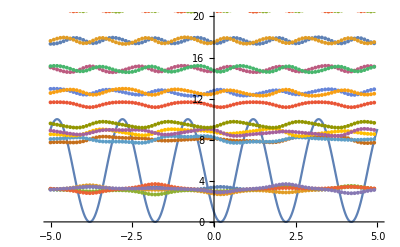

```mathematica
lat[x_]=10 Sin[Pi (x-0.1 2)/2]^2;
latham=periodichamiltonian[lat,xmin,xmax,dx];
latstates=Sort@Transpose[Eigensystem[latham,20,Method->{"Arnoldi","Shift"->0}]];
Show[Plot[lat[x],{x,-5,5}],ListPlot[Transpose[{xgrid,#1+2 #2}]&@@@latstates],PlotRange->{0,20}]
```

Take band (corresponding to the lowest 5 states)

```mathematica
Dimensions[firstband=latstates[[1;;5,2]]]
```

{5,100}

Periodic version of position operator: exponentiate.  Choose period to be size of cell.

```mathematica
expX=SparseArray[Band[{1,1}]->Exp[2 Pi I xgrid/10]];
ArrayPlot[Re[expX]]
```

-Graphics-

```mathematica
projexpX=firstband.expX.ConjugateTranspose[firstband]; (*project into lowest band *)
normsq=ConjugateTranspose[projexpX].projexpX; (* in finite system this projected operator is not unitary *)
norm=MatrixPower[normsq,-1/2];
nprojexpX=projexpX.norm   (* unitary version of projected operator *);
```

Find eigenstates and eigenvalues:  Eigenvalues are exponentials of the positions of Wannier States.  Eigenvectors are Wannier states.

```mathematica
firstes=Eigensystem[nprojexpX] //Chop
```

{{-0.728969-0.684547 ⅈ,0.992115+0.125333 ⅈ,0.425779-0.904827 ⅈ,0.187381+0.982287 ⅈ,-0.876307+0.481754 ⅈ},{{0.447214,0.596508,-0.210187,-0.556207,0.301054},{-0.447214,0.60613,0.180573,0.458197,0.435954},{-0.447214,0.0155692,0.632264,-0.626936,-0.0833728},{0.447214,-0.35904,0.520664,0.114442,0.622015},{-0.447214,-0.384231,-0.502361,-0.273026,0.570488}}}

Eigenvalues have complex phases, telling us where center of each Wannier state is:

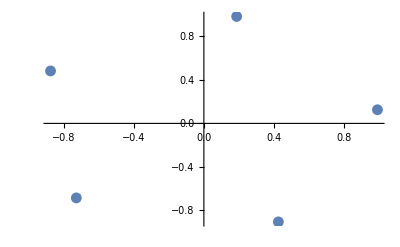

```mathematica
ListPlot[{Re[#],Im[#]}&/@firstes[[1]]]
```

As you would expect, states are evenly spaced.  See this by taking power:

```mathematica
firstes[[1]]^5 //Chop
```

{0.809017+0.587785 ⅈ,0.809017+0.587785 ⅈ,0.809017+0.587785 ⅈ,0.809017+0.587785 ⅈ,0.809017+0.587785 ⅈ}

Center of each Wannier state is shifted 10% of a lattice constant from the origin

```mathematica
Arg[firstes[[1]]^5]/(2 Pi)
```

{0.1,0.1,0.1,0.1,0.1}

Raise projected exponential of X to the number of sites -- get something proportional to the identity!!

```mathematica
MatrixPower[nprojexpX,5]//Chop //MatrixForm
```

(0.809017+0.587785 ⅈ | 0 | 0 | 0 | 0
0 | 0.809017+0.587785 ⅈ | 0 | 0 | 0
0 | 0 | 0.809017+0.587785 ⅈ | 0 | 0
0 | 0 | 0 | 0.809017+0.587785 ⅈ | 0
0 | 0 | 0 | 0 | 0.809017+0.587785 ⅈ)

Express Wannier states in original basis

```mathematica
XStatesInOriginalBasisper=firstes[[2]].firstband;
```

Algorithm gives random +-1’s multiplying wavefunction

```mathematica
Plus@@@XStatesInOriginalBasisper
```

{3.92408,-3.92408,-3.92408,3.92408,-3.92408}

Correct Phases to all be the same

```mathematica
phaseshifted = # Exp[-I Arg[Plus@@#]]&/@XStatesInOriginalBasisper;
```

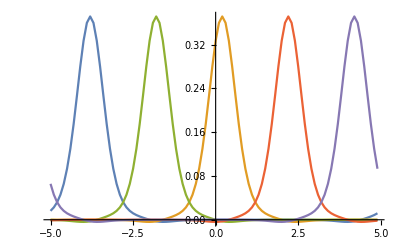

```mathematica
ListPlot[Transpose[{xgrid,# }]&/@phaseshifted,Joined->True,PlotRange->All]
```

Effective Hamiltonian

```mathematica
ord=Ordering[Arg[firstes[[1]]]]
```

{1,3,2,4,5}

```mathematica
MatrixForm[Chop[phaseshifted[[ord]].latham.ConjugateTranspose[phaseshifted[[ord]]]]]
```

(3.15396 | -0.0371861 | 0.000716739 | 0.000716739 | -0.0371861
-0.0371861 | 3.15396 | -0.0371861 | 0.000716739 | 0.000716739
0.000716739 | -0.0371861 | 3.15396 | -0.0371861 | 0.000716739
0.000716739 | 0.000716739 | -0.0371861 | 3.15396 | -0.0371861
-0.0371861 | 0.000716739 | 0.000716739 | -0.0371861 | 3.15396)

## Traditional picture

Bloch States -- |k>

Projector into lowest band -- P=∑_k |k><k|

Position operator -- X

Smallest momentum translation operator -- e^(2π I X/L)

Unless q=k-2π/L, matrix element vanishes:
<k|e^(2π I X/L)|q>  =0, 
In thermodynamic limit diagonal elements are just phases:

<k|e^(2π I X/L)|k-2π I/L>  = e^(I (2 π /L)A_k)

Defines Berry Connection A_k

N-sites, L=Na.  
Apply the momentum translation operator N times -- get back to start

(P e^(2π I X/L) P)^N=∑_k |k>e^(i Φ)<k|

Berry Phase

Φ=(2π)/L∑_k A_k

Interpret in terms of center-of-mass location of Wannier States, |j>:  By definition, e^(2π I X/L) is diagonal in basis of Wannier states, with center of mass

<j|e^(2π I X/L)|j>   = e^(i 2π x_j/L)=e^(i 2 π (x_0+ j a)/L)

x_0  is offset of Wannier state

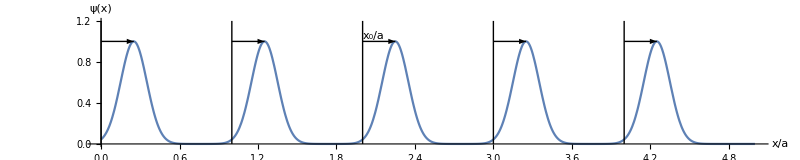

```mathematica
Plot[Sum[Exp[-50(x-j-0.25)^2],{j,0,4}],{x,0,5},PlotRange->{0,1.2},AxesLabel->{"x/a","ψ(x)"},BaseStyle->{FontSize->18},Epilog->{Table[{Line[{{j,0},{j,1.2}}],Arrowheads[0.02],Arrow[{{j,1},{j+0.25,1}}]},{j,0,4}],Text["x_0/a",{2,1},{-1.2,-1}]},ImageSize->800,AspectRatio->0.2]
```

Raise matrix element to n’th power

(<j|e^(2π I X/L)|j>)^N  = <j|(Pe^(2π I X/L)P)^N|j> = e^(i 2 π (x_0+ j a) N/L)=e^(i 2 π x_0/a)

This yields

Φ=2 π x_0/a

Position of Wanier state is given by a Berry Phase

## Calculational Stuff (Skip)

```mathematica
brickneighbors[{i_,j_}]= {{i+(-1)^(i+j),j},{i,j+1},{i,j-1}}
```

{{(-1)^(i+j)+i,j},{i,1+j},{i,-1+j}}

```mathematica
clockneighbors[{i_,j_}]={{i-(-1)^(i+j),j+(-1)^(i+j)},{i+(-1)^(i+j),j+(-1)^(i+j)},{i,j-2(-1)^(i+j)}}
```

{{(-1)^(1+i+j)+i,(-1)^(i+j)+j},{(-1)^(i+j)+i,(-1)^(i+j)+j},{i,-2 (-1)^(i+j)+j}}

```mathematica
counterclockneighbors[{i_,j_}]={{i+(-1)^(i+j),j-(-1)^(i+j)},{i-(-1)^(i+j),j-(-1)^(i+j)},{i,j+2(-1)^(i+j)}}
```

{{(-1)^(i+j)+i,(-1)^(1+i+j)+j},{(-1)^(1+i+j)+i,(-1)^(1+i+j)+j},{i,2 (-1)^(i+j)+j}}

```mathematica
hexpos[{i_,j_}]={3 i/2+(-1)^(i+j)/4,Sqrt[3] j/2}
```

{1/4 (-1)^(i+j)+(3 i)/2,(√3 j)/2}

```mathematica
index[{i_,j_},numy_]:= j+(i-1) numy
```

```mathematica
loc[ind_,numy_]:= {Quotient[ind,numy,1]+1, Mod[ind,numy,1]}
```

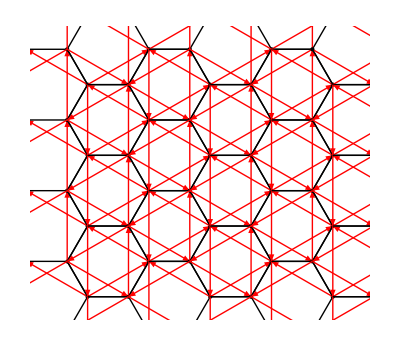

```mathematica
Show[Graphics[Table[{PointSize[Large],Point[hexpos[{i,j}]],Line[{hexpos[{i,j}],hexpos[#]}]&/@brickneighbors[{i,j}],
{Red,Arrow[{hexpos[{i,j}],hexpos[#]}]&/@clockneighbors[{i,j}]}
},{i,1,8},{j,1,8}]],PlotRange->{{0.5,8.5},{Sqrt[3]/4,8.5 Sqrt[3]/2}}]
```

```mathematica
xmat[numx_,numy_]:=SparseArray[Band[{1,1}]->Flatten[Table[hexpos[{i,j}][[1]],{i,1,numx},{j,1,numy}],1]]
```

```mathematica
ymat[numx_,numy_]:=SparseArray[Band[{1,1}]->Flatten[Table[hexpos[{i,j}][[2]],{i,1,numx},{j,1,numy}],1]]
```

```mathematica
xmat2[numx_,numy_]:=SparseArray[Band[{1,1}]->Flatten[Table[i,{i,1,numx},{j,1,numy}],1]]
```

```mathematica
ymat2[numx_,numy_]:=SparseArray[Band[{1,1}]->Flatten[Table[j,{i,1,numx},{j,1,numy}],1]]
```

```mathematica
transymat[numx_,numy_]:=SparseArray[Flatten[Table[{index[{i,j},numy],index[{i,Mod[j+2,numy,1]},numy]}->1,{i,1,numx},{j,1,numy}]],{numx numy,numx numy}]
```

```mathematica
transymat[2,6]//MatrixForm
```

(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0)

```mathematica
visualize[state_,numx_,numy_,scaling_]:=Table[{Disk[hexpos[{i,j}],scaling Abs[state[[index[{i,j},numy]]]]],Red,Arrow[{hexpos[{i,j}],hexpos[{i,j}]+scaling({Re[#],Im[#]}&@state[[index[{i,j},numy]]])}]},{i,1,numx},{j,1,numy}]
```

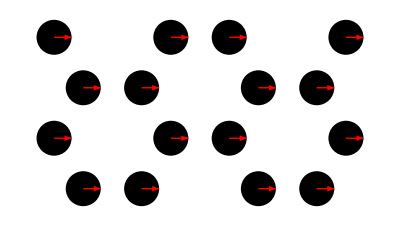

```mathematica
Show[Graphics[{Arrowheads[0.02],visualize[Table[1,{16}],4,4,0.3]}]]
```

```mathematica
perhaldaneham[numx_,numy_,t_,tprime_,delta_]:=
Module[{permap},
permap[{i_,j_}]={Mod[i,numx,1],Mod[j,numy,1]};
SparseArray[
Flatten[Table[{index[{i,j},numy],index[permap[#],numy]}->-t&/@brickneighbors[{i,j}],{i,1,numx},{j,1,numy}],2],{numx numy,numx numy}]+
SparseArray[
Flatten[Table[{index[{i,j},numy],index[permap[#],numy]}->-tprime&/@clockneighbors[{i,j}],{i,1,numx},{j,1,numy}],2],{numx numy,numx numy}]+
SparseArray[
Flatten[Table[{index[{i,j},numy],index[permap[#],numy]}->- Conjugate[tprime]&/@counterclockneighbors[{i,j}],{i,1,numx},{j,1,numy}],2],{numx numy,numx numy}]+
SparseArray[
Flatten[Table[{index[{i,j},numy],index[{i,j},numy]}->(-1)^(i+j) delta,{i,1,numx},{j,1,numy}],1],{numx numy,numx numy}]
]
```

```mathematica
hardhaldaneham[numx_,numy_,t_,tprime_,delta_]:=
Module[{isin},
isin[locs_]:=Cases[locs,{i_,j_}/;(i>0&&j>0&&i≤numx&&j≤numy)];
SparseArray[
Flatten[Table[{index[{i,j},numy],index[#,numy]}->-t&/@isin[brickneighbors[{i,j}]],{i,1,numx},{j,1,numy}],2],{numx numy,numx numy}]+
SparseArray[
Flatten[Table[{index[{i,j},numy],index[#,numy]}->-tprime&/@isin[clockneighbors[{i,j}]],{i,1,numx},{j,1,numy}],2],{numx numy,numx numy}]+
SparseArray[
Flatten[Table[{index[{i,j},numy],index[#,numy]}->-Conjugate[tprime]&/@isin[counterclockneighbors[{i,j}]],{i,1,numx},{j,1,numy}],2],{numx numy,numx numy}]+
SparseArray[
Flatten[Table[{index[{i,j},numy],index[{i,j},numy]}->(-1)^(i+j) delta,{i,1,numx},{j,1,numy}],1],{numx numy, numx numy}
]]
```

```mathematica
test1=hardhaldaneham[16,32,1,0.5I,0.]
```

SparseArray[<4292>, {512, 512}]

```mathematica
test2=perhaldaneham[16,32,1.,0.5I,0.]
```

SparseArray[<4608>, {512, 512}]

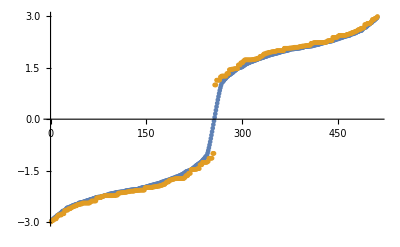

```mathematica
ListPlot[{ev1=Sort@Eigenvalues[Normal@test1],ev2=Chop@Sort@Eigenvalues[Normal@test2]}]
```

```mathematica
esys1=Transpose[Sort[Transpose[Eigensystem[test1,10,Method->{Arnoldi,Shift->0}]]]];
```

```mathematica
esys2=Transpose[Sort[Transpose[Eigensystem[test2,10,Method->{Arnoldi,Shift->0}]]]];
```

```mathematica
hardtopband=Transpose[Sort[Transpose[Eigensystem[test1,16*32/2,Method->{Arnoldi,Shift->-3}]]]];
```

```mathematica
pertopband=Transpose[Sort[Transpose[Eigensystem[test2,16*32/2,Method->{Arnoldi,Shift->-3}]]]];
```

```mathematica
allper=Transpose[Sort[Transpose[Eigensystem[Normal[test2]]]]]; (*Arnoldi does not orthogonalize properly in periodic case-- so just use dense matrices*)
```

```mathematica
allper[[1]]
```

{-3.,-2.96158,-2.96158,-2.94882,-2.94882,-2.9108,-2.9108,-2.9108,-2.9108,-2.84835,-2.84835,-2.79793,-2.79793,-2.79793,-2.79793,-2.79793,-2.79793,-2.76283,-2.76283,-2.76283,-2.76283,-2.66952,-2.66952,-2.6561,-2.6561,-2.6561,-2.6561,-2.61699,-2.61699,-2.61699,-2.61699,-2.58921,-2.58921,-2.56562,-2.56562,-2.55553,-2.55553,-2.53052,-2.53052,-2.53052,-2.53052,-2.49685,-2.49685,-2.49685,-2.49685,-2.47714,-2.47714,-2.47714,-2.47714,-2.44949,-2.44949,-2.44949,-2.44949,-2.44949,-2.44949,-2.44949,-2.44949,-2.44949,-2.44949,-2.44949,-2.44949,-2.42227,-2.42227,-2.38896,-2.38896,-2.38896,-2.38896,-2.38896,-2.38896,-2.38896,-2.38896,-2.2993,-2.2993,-2.2993,-2.2993,-2.29108,-2.29108,-2.29108,-2.29108,-2.25216,-2.25216,-2.25216,-2.25216,-2.23677,-2.23677,-2.23607,-2.23607,-2.23607,-2.23607,-2.23607,-2.23607,-2.23607,-2.23607,-2.23607,-2.23607,-2.23607,-2.23607,-2.23477,-2.23477,-2.23477,-2.23477,-2.2168,-2.2168,-2.2168,-2.2168,-2.15937,-2.15937,-2.15937,-2.15937,-2.14917,-2.14917,-2.14917,-2.14917,-2.14028,-2.14028,-2.13501,-2.13501,-2.13501,-2.13501,-2.12058,-2.12058,-2.12058,-2.12058,-2.10368,-2.10368,-2.10181,-2.10181,-2.101,-2.101,-2.101,-2.101,-2.08237,-2.08237,-2.08237,-2.08237,-2.0767,-2.0767,-2.0767,-2.0767,-2.07193,-2.07193,-2.07193,-2.07193,-2.07193,-2.07193,-2.07193,-2.07193,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-1.97911,-1.97911,-1.97911,-1.97911,-1.96711,-1.96711,-1.96711,-1.96711,-1.95413,-1.95413,-1.95413,-1.95413,-1.93193,-1.93193,-1.93193,-1.93193,-1.90511,-1.90511,-1.90511,-1.90511,-1.8626,-1.8626,-1.83285,-1.83285,-1.83285,-1.83285,-1.77981,-1.77981,-1.77981,-1.77981,-1.75732,-1.75732,-1.75732,-1.75732,-1.73998,-1.73998,-1.73998,-1.73998,-1.73205,-1.73205,-1.73205,-1.73205,-1.73205,-1.73205,-1.73205,-1.73205,-1.73205,-1.73205,-1.73205,-1.73205,-1.69908,-1.69908,-1.64705,-1.64705,-1.64705,-1.64705,-1.58348,-1.58348,-1.58348,-1.58348,-1.47363,-1.47363,-1.47363,-1.47363,-1.47363,-1.47363,-1.46222,-1.46222,-1.46222,-1.46222,-1.44423,-1.44423,-1.44423,-1.44423,-1.33249,-1.33249,-1.33249,-1.33249,-1.25948,-1.25948,-1.25948,-1.25948,-1.25928,-1.25928,-1.25928,-1.25928,-1.23367,-1.23367,-1.14214,-1.14214,-1.1396,-1.1396,-1.1396,-1.1396,-1.,-1.,-1.,1.,1.,1.,1.1396,1.1396,1.1396,1.1396,1.14214,1.14214,1.23367,1.23367,1.25928,1.25928,1.25928,1.25928,1.25948,1.25948,1.25948,1.25948,1.33249,1.33249,1.33249,1.33249,1.44423,1.44423,1.44423,1.44423,1.46222,1.46222,1.46222,1.46222,1.47363,1.47363,1.47363,1.47363,1.47363,1.47363,1.58348,1.58348,1.58348,1.58348,1.64705,1.64705,1.64705,1.64705,1.69908,1.69908,1.73205,1.73205,1.73205,1.73205,1.73205,1.73205,1.73205,1.73205,1.73205,1.73205,1.73205,1.73205,1.73998,1.73998,1.73998,1.73998,1.75732,1.75732,1.75732,1.75732,1.77981,1.77981,1.77981,1.77981,1.83285,1.83285,1.83285,1.83285,1.8626,1.8626,1.90511,1.90511,1.90511,1.90511,1.93193,1.93193,1.93193,1.93193,1.95413,1.95413,1.95413,1.95413,1.96711,1.96711,1.96711,1.96711,1.97911,1.97911,1.97911,1.97911,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.07193,2.07193,2.07193,2.07193,2.07193,2.07193,2.07193,2.07193,2.0767,2.0767,2.0767,2.0767,2.08237,2.08237,2.08237,2.08237,2.101,2.101,2.101,2.101,2.10181,2.10181,2.10368,2.10368,2.12058,2.12058,2.12058,2.12058,2.13501,2.13501,2.13501,2.13501,2.14028,2.14028,2.14917,2.14917,2.14917,2.14917,2.15937,2.15937,2.15937,2.15937,2.2168,2.2168,2.2168,2.2168,2.23477,2.23477,2.23477,2.23477,2.23607,2.23607,2.23607,2.23607,2.23607,2.23607,2.23607,2.23607,2.23607,2.23607,2.23607,2.23607,2.23677,2.23677,2.25216,2.25216,2.25216,2.25216,2.29108,2.29108,2.29108,2.29108,2.2993,2.2993,2.2993,2.2993,2.38896,2.38896,2.38896,2.38896,2.38896,2.38896,2.38896,2.38896,2.42227,2.42227,2.44949,2.44949,2.44949,2.44949,2.44949,2.44949,2.44949,2.44949,2.44949,2.44949,2.44949,2.44949,2.47714,2.47714,2.47714,2.47714,2.49685,2.49685,2.49685,2.49685,2.53052,2.53052,2.53052,2.53052,2.55553,2.55553,2.56562,2.56562,2.58921,2.58921,2.61699,2.61699,2.61699,2.61699,2.6561,2.6561,2.6561,2.6561,2.66952,2.66952,2.76283,2.76283,2.76283,2.76283,2.79793,2.79793,2.79793,2.79793,2.79793,2.79793,2.84835,2.84835,2.9108,2.9108,2.9108,2.9108,2.94882,2.94882,2.96158,2.96158,3.}

```mathematica
hardstates=hardtopband[[2]];
perstates=allper[[2,;;16 32/2]];
```

```mathematica
overlap=Chop@perstates.ConjugateTranspose[perstates]; (* check orthogonality*)
Max[Abs@overlap-IdentityMatrix[256]]
```

3.15096×10^-11

```mathematica
Dimensions[hardprojX=hardstates.xmat[16,32].ConjugateTranspose[hardstates]]
```

{256,256}

```mathematica
(hexpos[{16,1}]+hexpos[{16,2}])/2.
```

{24.,1.29904}

```mathematica
Dimensions[perprojX=perstates.MatrixExp[2 Pi I xmat[16,32]/24].ConjugateTranspose[perstates]]
```

{256,256}

```mathematica
Dimensions[projtransy=perstates.transymat[16,32].ConjugateTranspose[perstates]]
```

{256,256}

```mathematica
Max[Abs[perprojX.projtransy-projtransy.perprojX]]
```

1.66264×10^-14

```mathematica
normsqX=ConjugateTranspose[perprojX].perprojX; (* in finite system this projected operator is not unitary *)
normX=MatrixPower[normsqX,-1/2];
nperprojX=perprojX.normX   (* unitary version of projected operator *);
```

```mathematica
Dimensions[perprojX3=perstates.MatrixExp[2 Pi I xmat2[16,32]/16].ConjugateTranspose[perstates]]
normsqX3=ConjugateTranspose[perprojX3].perprojX3; (* in finite system this projected operator is not unitary *)
normX3=MatrixPower[normsqX3,-1/2];
nperprojX3=perprojX3.normX3   (* unitary version of projected operator *);
```

{256,256}

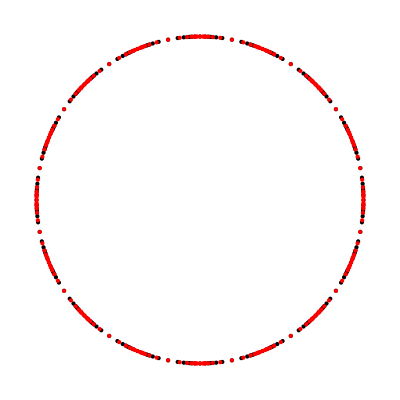

```mathematica
xev=Eigenvalues[nperprojX];
xev2=Eigenvalues[nperprojX3];
Show[Graphics[{Black,Point[{Re[#],Im[#]}&/@xev],Red,Point[{Re[#],Im[#]}&/@xev2]}],PlotRange->All]
```

```mathematica
Dimensions[hardprojY=hardstates.ymat[16,32].ConjugateTranspose[hardstates]]
```

{256,256}

```mathematica
(hexpos[{1,32}]+hexpos[{2,32}])/2
```

{9/4,16 √3}

```mathematica
Dimensions[perprojY=perstates.MatrixExp[2 Pi I ymat[16,32]/(16 Sqrt[3])].ConjugateTranspose[perstates]]
```

{256,256}

```mathematica
normsqY=ConjugateTranspose[perprojY].perprojY; (* in finite system this projected operator is not unitary *)
normY=MatrixPower[normsqY,-1/2];
nperprojY=perprojY.normY   (* unitary version of projected operator *);
```

```mathematica
Dimensions[perprojY3=perstates.MatrixExp[2 Pi I ymat2[16,32]/32].ConjugateTranspose[perstates]]
normsqY3=ConjugateTranspose[perprojY3].perprojY3; (* in finite system this projected operator is not unitary *)
normY3=MatrixPower[normsqY3,-1/2];
nperprojY3=perprojY3.normY3   (* unitary version of projected operator *);
```

{256,256}

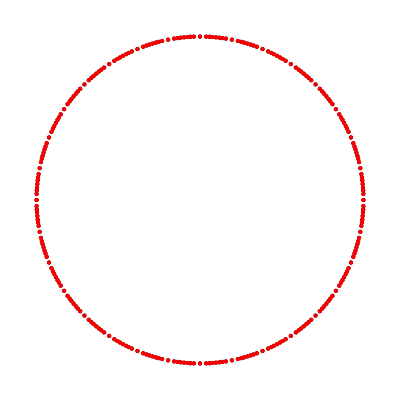

```mathematica
yev=Eigenvalues[nperprojY];
yev2=Eigenvalues[nperprojY3];
Show[Graphics[{Black,Point[{Re[#],Im[#]}&/@yev],Red,Point[{Re[#],Im[#]}&/@yev2]}],PlotRange->All]
```

```mathematica
hardcom=hardprojX.hardprojY-hardprojY.hardprojX;
```

```mathematica
percom=nperprojX.nperprojY-nperprojY.nperprojX;
```

```mathematica
percom3=nperprojX3.nperprojY3-nperprojY3.nperprojX3;
```

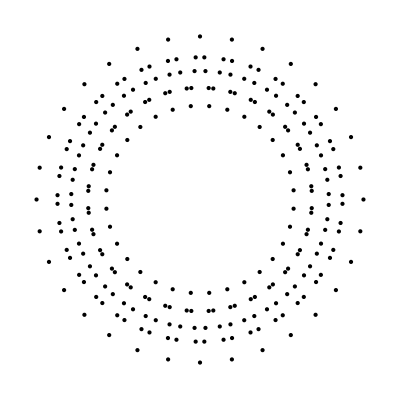

```mathematica
Show[Graphics[Point[{Re[#],Im[#]}&/@Eigenvalues[percom3]]],PlotRange->All]
```

```mathematica
Dimensions[hardcominoriginal=ConjugateTranspose[hardstates].hardcom.hardstates]
```

{512,512}

```mathematica
Dimensions[percominoriginal=ConjugateTranspose[perstates].percom.perstates]
```

{512,512}

```mathematica
Dimensions[percominoriginal3=ConjugateTranspose[perstates].percom3.perstates]
```

{512,512}

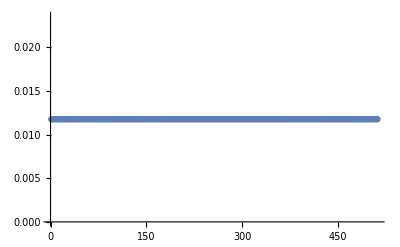

```mathematica
ListPlot[Abs[origperdiag3=Tr[percominoriginal3,List]]]
```

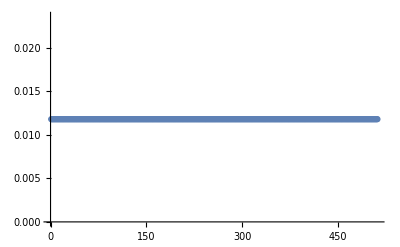

```mathematica
ListPlot[Abs[origperdiag=Tr[percominoriginal,List]],PlotRange->All]
```

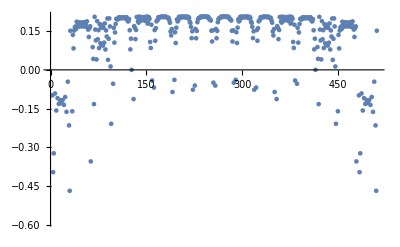

```mathematica
ListPlot[orighcdiag=Im[Tr[hardcominoriginal,List]//Chop]]
```

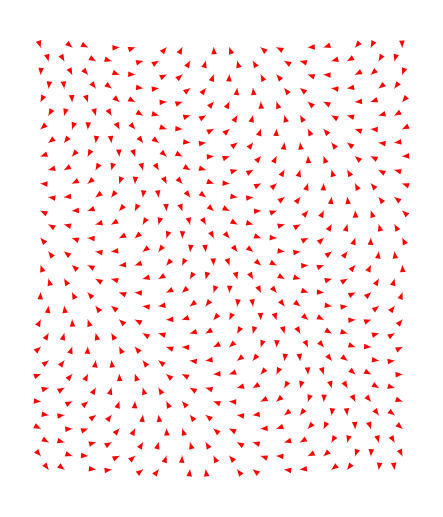

```mathematica
Show[Graphics[{Arrowheads[0.02],visualize[origperdiag,16,32,1]}]]
```

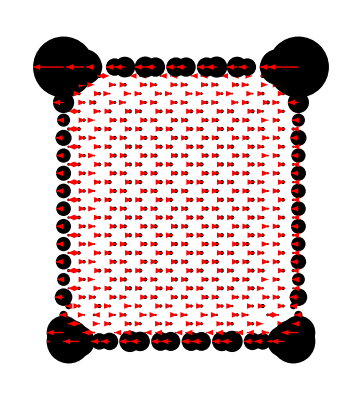

```mathematica
Show[Graphics[{Arrowheads[0.02],visualize[orighcdiag,16,32,1]}]]
```

```mathematica
?Manipulate
```

RowBox[{"Manipulate", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["u", "TI"], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] generates a version of StyleBox["expr", "TI"] with controls added to allow interactive manipulation of the value of StyleBox["u", "TI"]. 
RowBox[{"Manipulate", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["u", "TI"], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["max", "TI"]], ",", StyleBox["du", "TI"]}], "}"}]}], "]"}] allows the value of StyleBox["u", "TI"] to vary between SubscriptBox[StyleBox["u", "TI"], StyleBox["min", "TI"]] and SubscriptBox[StyleBox["u", "TI"], StyleBox["max", "TI"]] in steps StyleBox["du", "TI"]. 
RowBox[{"Manipulate", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{StyleBox["u", "TI"], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["init", "TI"]]}], "}"}], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["max", "TI"]], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] takes the initial value of StyleBox["u", "TI"] to be SubscriptBox[StyleBox["u", "TI"], StyleBox["init", "TI"]]. 
RowBox[{"Manipulate", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{StyleBox["u", "TI"], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["init", "TI"]], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["lbl", "TI"]]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] labels the controls for StyleBox["u", "TI"] with SubscriptBox[StyleBox["u", "TI"], StyleBox["lbl", "TI"]]. 
RowBox[{"Manipulate", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["u", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["u", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "}"}]}], "]"}] allows StyleBox["u", "TI"] to take on discrete values RowBox[{SubscriptBox[StyleBox["u", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}]. 
RowBox[{"Manipulate", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["u", "TI"], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["v", "TI"], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["…", "TR"]}], "]"}] provides controls to manipulate each of the RowBox[{StyleBox["u", "TI"], ",", StyleBox["v", "TI"], ",", StyleBox["…", "TR"]}]. 
RowBox[{"Manipulate", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{SubscriptBox[StyleBox["c", "TI"], StyleBox["u", "TI"]], "→", RowBox[{"{", RowBox[{StyleBox["u", "TI"], ",", StyleBox["…", "TR"]}], "}"}]}], ",", RowBox[{SubscriptBox[StyleBox["c", "TI"], StyleBox["v", "TI"]], "→", RowBox[{"{", RowBox[{StyleBox["v", "TI"], ",", StyleBox["…", "TR"]}], "}"}]}], ",", StyleBox["…", "TR"]}], "]"}] links the controls to the specified controllers on an external device.

```mathematica
Manipulate[
eigens=Eigensystem[Cos[θ]hardprojX+Sin[θ]hardprojY];
ord=Ordering[eigens[[1]]];
Show[Graphics[{Arrowheads[0.02],visualize[Conjugate[eigens[[2,ord[[j]]]]].hardstates,16,32,2]}]],{j,1,16*32/2,1},{θ,0,2 Pi}]
```

```mathematica
Manipulate[
eigens=Eigensystem[perprojX];
ord=Ordering[Arg[eigens[[1]]]];
Show[Graphics[{Arrowheads[0.02],visualize[Conjugate[eigens[[2,ord[[j]]]]].perstates,16,32,2]}]],{j,1,16*32/2,1}]
```

```mathematica
eigens=Eigensystem[perprojX+0*perprojY];
ord=Ordering[Arg[eigens[[1]]]]
```

{48,14,83,144,154,200,224,255,209,204,170,143,110,19,58,71,62,20,112,137,151,203,228,241,221,179,157,117,84,11,51,66,63,21,104,132,169,206,238,247,222,177,164,133,95,2,40,74,49,17,91,135,176,185,231,256,234,180,158,134,99,16,37,69,41,6,100,120,171,178,232,252,214,193,174,138,89,12,33,72,45,7,105,119,146,197,235,251,219,199,167,125,87,23,61,68,43,8,85,113,156,182,220,242,223,184,148,122,92,4,53,79,35,10,97,131,161,189,213,243,217,198,175,121,94,24,57,75,47,27,101,141,153,183,237,246,229,207,168,126,90,18,52,76,46,5,106,139,147,191,216,253,230,187,162,123,81,15,50,73,42,9,86,116,149,181,218,250,215,192,173,142,107,22,56,70,34,25,111,124,165,202,210,249,236,201,152,140,102,28,64,67,44,32,93,129,163,208,211,245,227,186,159,118,103,1,54,65,38,30,88,115,155,196,240,254,239,194,160,128,109,29,39,77,55,31,108,127,172,205,212,248,226,188,166,114,96,26,59,80,60,3,98,136,145,190,225,244,233,195,150,130,82,13,36,78}

```mathematica
Dimensions[eigens[[2,ord[[1]]]]]
```

{256}

```mathematica
Dimensions[eigens[[2,ord[[1]]]].perstates]
```

{512}

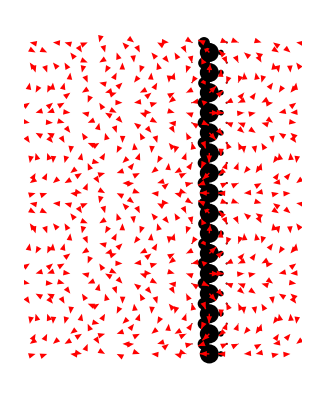

```mathematica
Show[Graphics[{Arrowheads[0.02],visualize[Conjugate[eigens[[2,ord[[50]]]]].perstates,16,32,4]}]]
```

```mathematica
xevs=Eigensystem[nperprojX];
```

```mathematica
Dimensions[xevs[[2]]]
```

{256,256}

```mathematica
xevs[[1,;;10]]
```

{0.96746+0.253023 ⅈ,-0.863012-0.505183 ⅈ,0.707107-0.707107 ⅈ,-0.55557-0.83147 ⅈ,0.19509+0.980785 ⅈ,-0.427495-0.904018 ⅈ,0.136468+0.990644 ⅈ,-0.890475+0.455032 ⅈ,-0.729188+0.684313 ⅈ,0.603994+0.796989 ⅈ}

```mathematica
MatrixForm@Take[Chop@Abs[ConjugateTranspose[xevs[[2]]].xevs[[2]]],10,10]
```

(1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.)

```mathematica
Max[Abs[nperprojX.projtransy-projtransy.nperprojX]]
```

1.48981×10^-14

```mathematica
Abs[Conjugate[xevs[[2,22]]].projtransy.xevs[[2,21]]]
```

3.31367×10^-16

```mathematica
simul=Conjugate[xevs[[2]]].projtransy.Transpose[xevs[[2]]];
```

```mathematica
xvals=Mod[Arg[xevs[[1]]],2 Pi];
```

```mathematica
kvals=Round[16Mod[Arg[Tr[simul,List]],2 Pi]/(2 Pi)];
```

```mathematica
ord=Ordering[Transpose[{kvals,xvals}]];
```

```mathematica
sortedstates=Partition[Conjugate[xevs[[2,ord]]].perstates,16];
```

### Cylinder

```mathematica
cylhaldaneham[numx_,numy_,t_,tprime_,delta_,chi_]:=
Module[{permap,isin,phase},
phase[{i1_,j1_},{i2_,j2_}]:=If[j2>numy,Exp[I chi],If[j2<1,Exp[-I chi],1]];
isin[locs_]:=Cases[locs,{i_,j_}/;(i>0&&i≤numx)];
permap[{i_,j_}]:={Mod[i,numx,1],Mod[j,numy,1]};
Plus@@(SparseArray[#,{numx numy,numx numy}]&/@
Flatten[Table[{index[{i,j},numy],index[permap[#],numy]}->-t phase[{i,j},#]&/@isin[brickneighbors[{i,j}]],{i,1,numx},{j,1,numy}],2])+
Plus@@(SparseArray[#,{numx numy,numx numy}]&/@
Flatten[Table[{index[{i,j},numy],index[permap[#],numy]}->-tprime phase[{i,j},#]&/@isin[clockneighbors[{i,j}]],{i,1,numx},{j,1,numy}],2])+
Plus@@(SparseArray[#,{numx numy,numx numy}]&/@
Flatten[Table[{index[{i,j},numy],index[permap[#],numy]}->- Conjugate[tprime] phase[{i,j},#]&/@isin[counterclockneighbors[{i,j}]],{i,1,numx},{j,1,numy}],2])+
SparseArray[
Flatten[Table[{index[{i,j},numy],index[{i,j},numy]}->(-1)^(i+j) delta,{i,1,numx},{j,1,numy}],1],{numx numy,numx numy}]
]
```

```mathematica
hxproj2[k_,tprime_,delta_]:=Module[{states=Sort[Transpose[Eigensystem[cylhaldaneham[16,2,1,tprime,delta,k]]]][[;;16,2]],projx,xev},projx=states.xmat[16,2].ConjugateTranspose[states];
xev=Sort[Transpose[Eigensystem[projx]]];
{xev[[All,1]],Conjugate[xev[[All,2]]].states}]
```

```mathematica
hlocs11=Table[{#,k}&/@hxproj2[k,0.3 I,0.][[1]],{k,-Pi+0.001,Pi,(Pi-0.001)/60}];
```

### Kane-Mele

```mathematica
rashba[numx_,numy_,alpha_,mu_,nu_]:=
Module[{isin},
isin[locs_]:=Cases[locs,{i_,j_}/;(i>0&&j>0&&i≤numx&&j≤numy)];
SparseArray[
Flatten[Table[{index[{i,j},numy],index[#,numy]}->-alpha (hexpos[#]-hexpos[{i,j}]).({sigmay[[mu,nu]],-sigmax[[mu,nu]]})&/@isin[brickneighbors[{i,j}]],{i,1,numx},{j,1,numy}],2],{numx numy,numx numy}]]
```

```mathematica
kanemeleham[numx_,numy_,t_,tprime_(*spin-orbit should be imaginary*),delta_,alpha_ (*Rashba -- should be imaginary*)]:=
ArrayFlatten[{{hardhaldaneham[numx,numy,t,tprime,delta],rashba[numx,numy,alpha,1,2]},
{rashba[numx,numy,alpha,2,1],hardhaldaneham[numx,numy,t,Conjugate[tprime],delta]}}]
```

```mathematica
cylrashba[numx_,numy_,alpha_,mu_,nu_,chi_]:=
Module[{permap,isin,phase},
phase[{i1_,j1_},{i2_,j2_}]:=If[j2>numy,Exp[I chi],If[j2<1,Exp[-I chi],1]];
isin[locs_]:=Cases[locs,{i_,j_}/;(i>0&&i≤numx)];
permap[{i_,j_}]:={Mod[i,numx,1],Mod[j,numy,1]};
Plus@@(SparseArray[#,{numx numy,numx numy}]&/@
Flatten[Table[{index[{i,j},numy],index[permap[#],numy]}->-alpha (hexpos[#]-hexpos[{i,j}]).({sigmay[[mu,nu]],-sigmax[[mu,nu]]})phase[{i,j},#]&/@isin[brickneighbors[{i,j}]],{i,1,numx},{j,1,numy}],2])]
```

```mathematica
cylkanemeleham[numx_,numy_,t_,tprime_(*spin-orbit should be imaginary*),delta_,alpha_ (*Rashba -- should be imaginary*),chi_]:=
ArrayFlatten[{{cylhaldaneham[numx,numy,t,tprime,delta,chi],cylrashba[numx,numy,alpha,1,2,chi]},
{cylrashba[numx,numy,alpha,2,1,chi],cylhaldaneham[numx,numy,t,Conjugate[tprime],delta,chi]}}]
```

```mathematica
kmxmat[numx_,numy_]:=SparseArray[Band[{1,1}]->Join[#,#]&@Flatten[Table[hexpos[{i,j}][[1]],{i,1,numx},{j,1,numy}],1]]
```

```mathematica
kmproj[k_,tprime_,delta_,alpha_]:=Module[{states=Sort[Transpose[Eigensystem[cylkanemeleham[16,2,1,tprime,delta,alpha,k]]]][[;;32,2]],projx,xev},projx=states.kmxmat[16,2].ConjugateTranspose[states];
xev=Sort[Transpose[Eigensystem[projx]]];
{xev[[All,1]],Conjugate[xev[[All,2]]].states}]
```

```mathematica
kmlocs11=Table[{#,k}&/@kmproj[k,0.3 I,0.,0.2 I][[1]],{k,-Pi+0.001,Pi,(Pi-0.002)/80}];
```

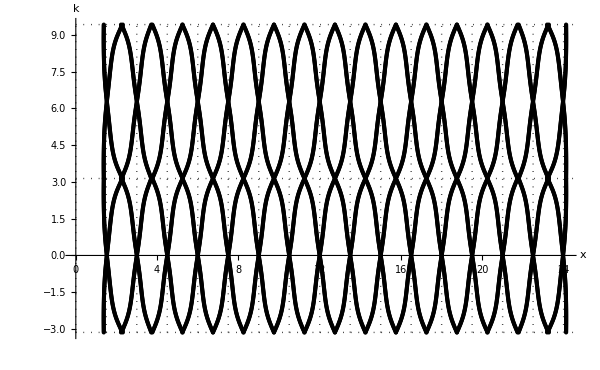

```mathematica
ListPlot[Join[Transpose[Re@kmlocs11],Transpose[Re@kmlocs11]/.{a_,b_}->{a,b+2 Pi}],Joined->False,PlotStyle->{{PointSize[Small],Thick,Black}},ImageSize->600,BaseStyle->{FontSize->16},
AxesLabel->{"x","k"},Epilog->{Dotted,Table[Line[{{0,j},{30,j}}],{j,-Pi,6 Pi,2 Pi}],
Table[Line[{{j,-Pi},{j,3 Pi}}],{j,0,30,1.5}]
}]
```

```mathematica
kmlocs12=Table[{#,k}&/@kmproj[k,0.1 I,1.,0.2 I][[1]],{k,-Pi+0.001,Pi,(Pi-0.002)/80}];
```

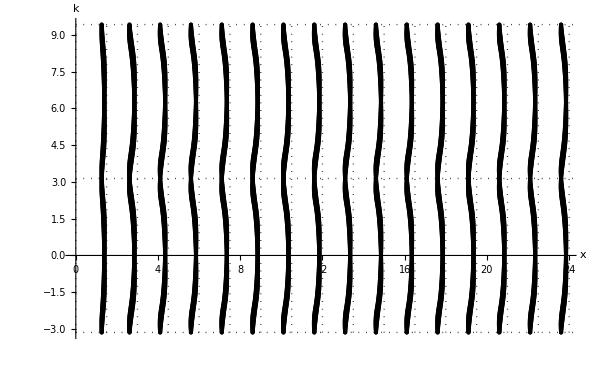

```mathematica
ListPlot[Join[Transpose[Re@kmlocs12],Transpose[Re@kmlocs12]/.{a_,b_}->{a,b+2 Pi}],Joined->False,PlotStyle->{{PointSize[Small],Thick,Black}},ImageSize->600,BaseStyle->{FontSize->16},
AxesLabel->{"x","k"},Epilog->{Dotted,Table[Line[{{0,j},{30,j}}],{j,-Pi,6 Pi,2 Pi}],
Table[Line[{{j,-Pi},{j,3 Pi}}],{j,0,30,1.5}]
}]
```

```mathematica
hxproj2[k_,tprime_,delta_]:=Module[{states=Sort[Transpose[Eigensystem[cylhaldaneham[16,2,1,tprime,delta,k]]]][[;;16,2]],projx,xev},projx=states.xmat[16,2].ConjugateTranspose[states];
xev=Sort[Transpose[Eigensystem[projx]]];
{xev[[All,1]],Conjugate[xev[[All,2]]].states}]
```

```mathematica
hlocs11=Table[{#,k}&/@hxproj2[k,0.3 I,0.][[1]],{k,-Pi+0.001,Pi,(Pi-0.001)/60}];
```

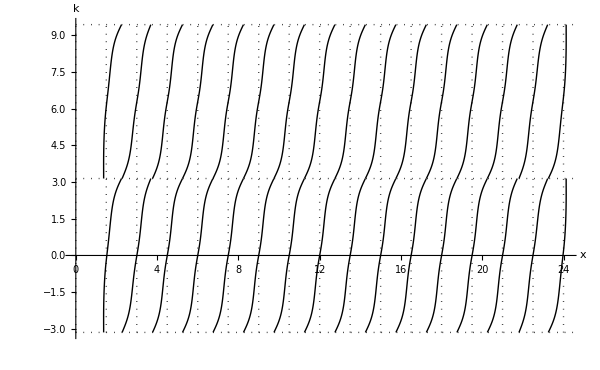

```mathematica
ListPlot[Join[Transpose[Re@hlocs11],Transpose[Re@hlocs11]/.{a_,b_}->{a,b+2 Pi}],Joined->True,PlotStyle->{{Thick,Black}},ImageSize->600,BaseStyle->{FontSize->16},
AxesLabel->{"x","k"},Epilog->{Dotted,Table[Line[{{0,j},{30,j}}],{j,-Pi,6 Pi,2 Pi}],
Table[Line[{{j,-Pi},{j,3 Pi}}],{j,0,30,1.5}]
}]
```

## 2D version

Haldane model:  honeycomb lattice.  Hopping on black bonds is real, hopping on red is complex.  2-bands

```mathematica
Show[Graphics[Table[{PointSize[Large],Point[hexpos[{i,j}]],Line[{hexpos[{i,j}],hexpos[#]}]&/@brickneighbors[{i,j}],
{Red,Arrow[{hexpos[{i,j}],hexpos[#]}]&/@clockneighbors[{i,j}]}
},{i,1,8},{j,1,8}]],PlotRange->{{0.5,8.5},{Sqrt[3]/4,8.5 Sqrt[3]/2}}]
```

-Graphics-

As before, conceptually cleanest in finite system.

Project X-position operator into lowest band.  Find eigenstates

```mathematica
eigens=Eigensystem[hardprojX];
ord=Ordering[eigens[[1]]];
Manipulate[
Show[Graphics[{Arrowheads[0.02],visualize[Conjugate[eigens[[2,ord[[x]]]]].hardstates,16,32,4]}]],{x,1,16*32/2,1}]
```

Project Y-position operator into lowest band.  Find eigenstates

```mathematica
yeigens=Eigensystem[hardprojY];
yord=Ordering[yeigens[[1]]];
Manipulate[
Show[Graphics[{Arrowheads[0.02],visualize[Conjugate[yeigens[[2,yord[[y]]]]].hardstates,16,32,4]}]],{y,1,16*32/2,1}]
```

Problem: projected X and do not Commute

```mathematica
ArrayPlot[commutator=ConjugateTranspose[hardstates].(hardprojX.hardprojY-hardprojY.hardprojX).hardstates]
```

-Graphics-

In bulk, diagonal elements of projected [X,Y] are constant: related to Chern number.  Morally:  [X,Y]=const -- X and Y (projected into lowest band) are conjugate variables

Visual display of diagonal elements :

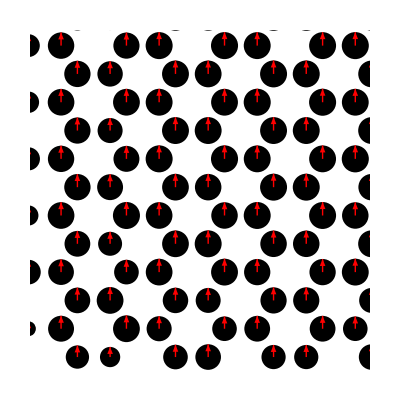

```mathematica
Show[Graphics[{Arrowheads[0.02],visualize[Tr[commutator,List],16,32,2]}],PlotRange->{{5,15},{5,15}}]
```

More Structure at Edge:

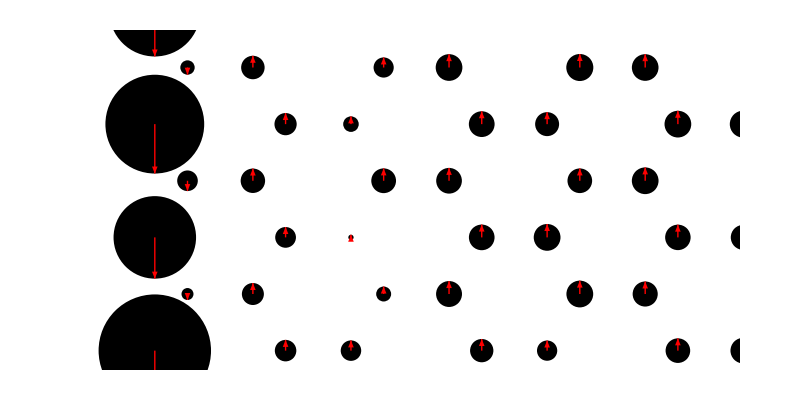

```mathematica
Show[Graphics[{Arrowheads[0.01],visualize[Tr[commutator,List],16,32,1]}],PlotRange->{{0,10},{5,10}},ImageSize->800]
```

Upshot: Cannot find simultaneous eigenstates of projected X and Y operators.  In some very real sense Wannier states do not exist for a 2D band with finite Chern number.  You cannot make a single-band tight-binding model with finite Chern number.

## Conditional Wannier states

Idea: Fix k_y then get an effective 1D system.  Find its Wannier States:  ψ(k_y,x)

Hall effect:  Applying a force in y-direction (changing ky) shifts particles in x-direction.

Plot Simultaneous eigenstates of y-translation operator, and x projected into lowest band:

```mathematica
Manipulate[
Show[Graphics[{Arrowheads[0.02],visualize[sortedstates[[k,x]],16,32,3]}],PlotRange->{{0,10},{0,10}}],{k,1,16,1},{x,1,16,1}]
```

Increase k_yby 2π: Wannier states map onto themselves.

Plot Center of mass of Wannier states as a function of k_y
[Periodic boundary in y, hard wall in x]

```mathematica
ListPlot[Join[Transpose[Re@hlocs11],Transpose[Re@hlocs11]/.{a_,b_}->{a,b+2 Pi}],Joined->True,PlotStyle->{{Thick,Black}},ImageSize->600,BaseStyle->{FontSize->16},
AxesLabel->{"x","k"},Epilog->{Dotted,Table[Line[{{0,j},{30,j}}],{j,-Pi,6 Pi,2 Pi}],
Table[Line[{{j,-Pi},{j,3 Pi}}],{j,0,30,1.5}]
}]
```

-Graphics-

Edge states must exist:  Wannier states must go somewhere when they reach edge of sample

## Homotopy

Let P(k_y) project into sector of the lowest band with fixed k_y

Let P(k_y)X P(k_y) be the position operator projected into this space

Smallest X-momentum translation operator in this subspace: P(k_y)e^(2π I X/L)P(k_y)

Raise to N’th power, get phase factor: [P(k_y)e^(2π I X/L)P(k_y)]^N=e^(i ϕ(k_y)) P(k_y)

Center of mass of each Wannier state (relative to unit cell) is ϕ(k_y)

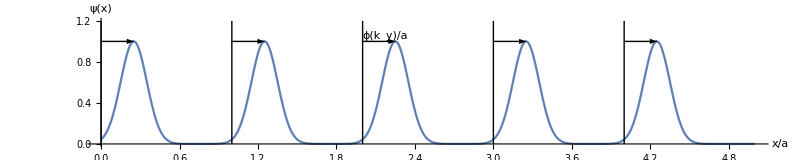

```mathematica
Plot[Sum[Exp[-50(x-j-0.25)^2],{j,0,4}],{x,0,5},PlotRange->{0,1.2},AxesLabel->{"x/a","ψ(x)"},BaseStyle->{FontSize->18},Epilog->{Table[{Line[{{j,0},{j,1.2}}],Arrowheads[0.02],Arrow[{{j,1},{j+0.25,1}}]},{j,0,4}],Text["ϕ(k_y)/a",{2,1},{-1.2,-1}]},ImageSize->800,AspectRatio->0.2]
```

Increase k_yby 2π:  U=e^(i ϕ(k_y)) must map back onto itself.

Classify 2D bandstructure by non-equivalent maps of circle into space of phases:  π_1(U(1))  These are just integers.

```mathematica
Manipulate[Show[Graphics[{Table[Line[{{i,0},{i+j,2}}],{i,-4,8}],
PointSize[Large],Table[{Point[{i,0}],Point[{i,2}]},{i,0,5}]
}],Axes->True,AxesLabel->{"Center of Wannier State","ky"},ImageSize->800,BaseStyle->{FontSize->16},Ticks->None,PlotRange->{{0,5},{0,2}}],Control[{{j,0},-3,3,1}]]
```

## Spin

Wannier states have spin structure

Smallest X-momentum translation operator in subspace of fixed k_y: P(k_y)e^(2π I X/L)P(k_y)

Raise to N’th power (N is number of lattice periods in x-direction), yields unitary unitary matrix in spin space: [P(k_y)e^(2π I X/L)P(k_y)]^N= O P(k_y)

O will be a 2x2 unitary matrix in spin space.  Band structures are then classified by maps of circles into space of unitary 2x2 matrices:  This is trivial, as --  π_1(U(2))=0.  Thus, once you add spin, the Wannier states no longer distinguish different bands.

Add symmetries (ex, time reversal invarience), reduces the allowed possibilities.

### Equivalent viewpoint

All Wannier states at fixed k_yare translations of two wavefunctions: ψ_1(x,σ) and ψ_2(x,σ)

Follow center of mass of these two states.  Whenever they touch, they can mix, letting you “unwind” knots.  Any two configurations can be smoothly connected,

```mathematica
oneone[sep_]:=Show[Graphics[{{Thick,Blue,Table[Line[Table[{j+k+0.5 k(1-k),k},{k,0,1,0.1}]],{j,0,5}]},{Thick,Black,Table[Line[Table[{j+k-0.5k(1-k)+sep,k},{k,0,1,0.1}]],{j,0,5}]},{Dotted,
Table[Line[{{j,0},{j,1}}],{j,0,6,1}],Table[Line[{{j+sep,0},{j+sep,1}}],{j,0,6,1}]}
}],ImageSize->600,PlotRange->{{1,5.01},{0,1}},Ticks->None,Axes->True,AxesLabel->{"x","k"},BaseStyle->{FontSize->16}];
onetwo[sep_]:=Show[Graphics[{{Thick,Blue,Table[Line[Table[{j+k(1+sep)+0.5 k(1-k),k},{k,0,1,0.1}]],{j,0,5}]},{Thick,Black,Table[Line[Table[{j+k-0.5k(1-k)+sep(1-k),k},{k,0,1,0.1}]],{j,0,5}]},{Dotted,
Table[Line[{{j,0},{j,1}}],{j,0,6,1}],Table[Line[{{j+sep,0},{j+sep,1}}],{j,0,6,1}]}
}],ImageSize->600,PlotRange->{{1,5.01},{0,1}},Ticks->None,Axes->True,AxesLabel->{"x","k"},BaseStyle->{FontSize->16}];
twotwo[curve_]:=Show[Graphics[{{Thick,Blue,Table[Line[Table[{j-k+curve k(1-k),k},{k,0,1,0.1}]],{j,0,5}]},{Thick,Black,Table[Line[Table[{j+k-curve k(1-k)-2(1-k),k},{k,0,1,0.1}]],{j,0,5}]},{Dotted,
Table[Line[{{j,0},{j,1}}],{j,0,6,1}]}
}],ImageSize->600,PlotRange->{{1,5.01},{0,1}},Ticks->None,Axes->True,AxesLabel->{"x","k"},BaseStyle->{FontSize->16}];
twothree[sep_]:=Show[Graphics[{{Thick,Blue,Table[Line[{{j,0},{j-1/2+sep,1/2},{j+1/4-sep/2,3/4},{j,1}}],{j,0,5}]},{Thick,Black,Table[Line[{{j,0},{j+1.5-sep,1/2},{j+1.25+sep/2,3/4},{j+2,1}}],{j,0,5}]},{Dotted,
Table[Line[{{j,0},{j,1}}],{j,0,6,1}]}
}],ImageSize->600,PlotRange->{{1,5.01},{0,1}},Ticks->None,Axes->True,AxesLabel->{"x","k"},BaseStyle->{FontSize->16}];
twofour[sep_]:=Show[Graphics[{{Thick,Blue,Table[Line[Table[{j-0.5 sep k(1-k)+(1-k)sep,k},{k,0,1,0.1}]],{j,0,5}]},{Thick,Black,Table[Line[Table[{j+2k+0.5sep k(1-k)+sep k,k},{k,0,1,0.1}]],{j,0,5}]},{Dotted,
Table[Line[{{j,0},{j,1}}],{j,0,6,1}],Table[Line[{{j+sep,0},{j+sep,1}}],{j,0,6,1}]}
}],ImageSize->600,PlotRange->{{1,5.01},{0,1}},Ticks->None,Axes->True,AxesLabel->{"x","k"},BaseStyle->{FontSize->16}];
frames=Join[Table[oneone[sep],{sep,0.5,0,-0.05}],Table[onetwo[sep],{sep,0,-2,-0.05}],Table[twotwo[curve],{curve,0.5,0,-0.1}],Table[twothree[sep],{sep,0.,0.5,0.05}],Table[twofour[sep],{sep,0.,-2.,-0.05}]];
Manipulate[frames[[j]],{j,1,Length[frames],1}]
```

## Time-reversal symmetry

Time reversal symmetry enforces: center of mass of ψ_1(k_y)= center of mass of ψ_2(-k_y)  (modulo lattice spacing)

x_1(k_y)=x_2(-k_y) mod a

Two crossing points: k_y=0,π --  x_1(0)=x_2(0)      and  x_1(π)=x_2(π) mod a

With constraint that the centers of masses agree at these two points, there are exactly two inequivalent configurations.

Nontrivial:

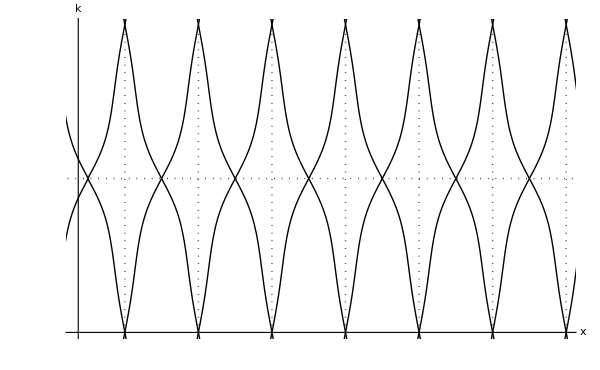

```mathematica
ListPlot[Join[Transpose[Re@kmlocs11],Transpose[Re@kmlocs11]/.{a_,b_}->{a,b+2 Pi}],Joined->True,PlotStyle->{{PointSize[Small],Thick,Black}},ImageSize->600,BaseStyle->{FontSize->16},
AxesLabel->{"x","k"},Epilog->{Dotted,Table[Line[{{0,j},{30,j}}],{j,-Pi,6 Pi,2 Pi}],
Table[Line[{{j,-Pi},{j,3 Pi}}],{j,0,30,1.5}]},Ticks->None,PlotRange->{{5,15},{0,2 Pi}}]
```

Trivial:

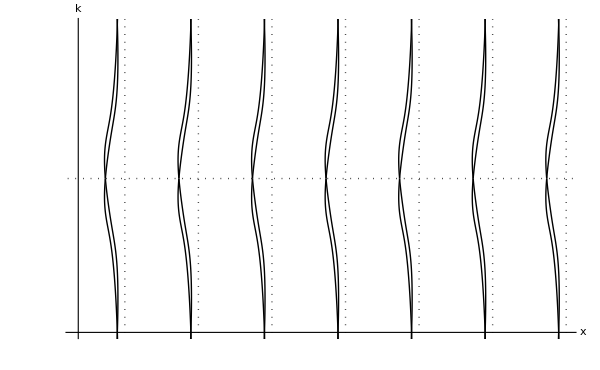

```mathematica
ListPlot[Join[Transpose[Re@kmlocs12],Transpose[Re@kmlocs12]/.{a_,b_}->{a,b+2 Pi}],Joined->True,PlotStyle->{{PointSize[Small],Thick,Black}},ImageSize->600,BaseStyle->{FontSize->16},
AxesLabel->{"x","k"},Epilog->{Dotted,Table[Line[{{0,j},{30,j}}],{j,-Pi,6 Pi,2 Pi}],
Table[Line[{{j,-Pi},{j,3 Pi}}],{j,0,30,1.5}]
},Ticks->None,PlotRange->{{5,15},{0,2 Pi}}]
```

## Higher dimension

Location of x-Wannier states become function of k_y and k_z

Classify by maps of torus into  U(1) :  Z×Z

## Summary

1D: Wannier states are eigenstates of position operator projected into band

Eigenvalues are center-of-mass positions

Evenly spaced

Offset from Origin = Zac Phase

2D: Projected X and P operators do not commute

No natural way to define 2D Wannier states if Chern number is finite

Projected X and k_y commute

1D Wannier states are function of k_y

Chern number = how many lattice sites Wannier State moves when you increment k_y by 2π

Spin: Projected X operator becomes matrix in spin-space

All braids can be untwisted

Add time-reversal invariance: 2 inequivalent braids

Higher Dimension:  X-Wannier states become function of k_y and k_z